```mathematica
MyInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
```

```mathematica
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
```

```mathematica
ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K]
```

```mathematica
SBTM[s_,nb_,limit_]:=Module[{k=2,tm},{tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

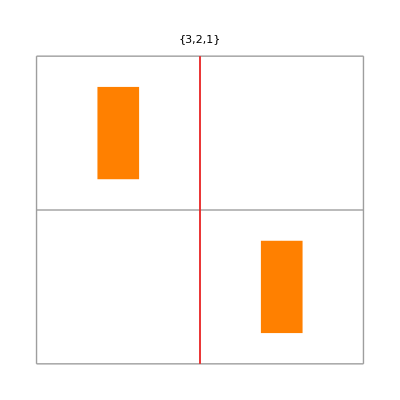

```mathematica
SBTM[3,1,21]
```

```mathematica
SBTM[3,1812450,21]        (*1812450 se comprend dans ma numérotation*)
```

-Graphics-

```mathematica
SingleTMEvolveList[WolframInstructionsTable[1812450,{3,2}],{},21]
```

{{1,{},1},{2,{1},2},{3,{1,1},3},{1,{1,1,1},2},{2,{1,0,1},1},{2,{1,0,0},2},{3,{1,1,0},3},{2,{1,1,0},2},{2,{1,0,0},3},{2,{0,0,0},4},{3,{1,0,0,0},5},{1,{1,1,0,0,0},4},{2,{1,0,0,0,0},3},{3,{1,0,1,0,0},4},{1,{1,1,1,0,0},3},{2,{1,1,0,0,0},2},{3,{1,1,0,1,0},3},{1,{1,1,1,1,0},2},{2,{1,1,1,0,0},1},{3,{1,1,1,0,1},2},{1,{1,1,1,1,1},1},{2,{1,1,1,1,0},0}}